NDSolveValue::ibcinc: Warning: boundary and initial conditions are inconsistent.

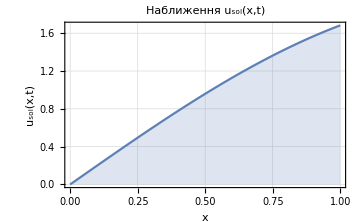
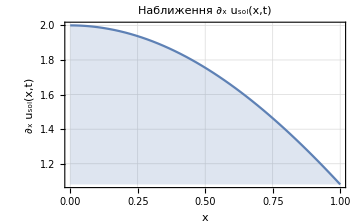

‖u_sol‖_0=1.04437												‖u_sol‖_1=2.

```mathematica
a=0;b=1;deltat = 0.1;
μ[x_]:=1;β[x_]:=0;σ[x_]:=0;
u0 = 0; u1 = Cos[1];
ψ[x_,t_]=1/(t+1)*Sin[x];
ufirst[x_]=Sin[x]+ψ[x,0];
f[x_,t_]:=Sin[x]*(t^2+3*t+1)/(1+t)^2;
Subscript[t, begin]=0;Subscript[t, max]=25;
$MaxPiecewiseCases=700;
(*Точний розвязок диф рівняння*)
Subscript[u, sol]=NDSolveValue[{D[u[x,t], t]-(D[μ[x], x]*D[u[x,t], x]+μ[x] *D[u[x,t], x,x])+β[x]* D[u[x,t], x]+σ[x] *u[x,t]==f[x,t],u[0,t]==u0,Derivative[1,0][u][1,t]==u1, u[x,0]==ufirst[x]},u,{x,a,b},{t,Subscript[t, begin]}];
Subscript[plot1u, sol]=Plot[Subscript[u, sol][x,Subscript[t, begin]],{x,a,b},FrameLabel->{"x ","u_sol(x,t) "},PlotLabel->Style[Framed["Наближення u_sol(x,t)"]],Background->White,Filling->Axis,Frame->True,GridLines->Automatic,PlotRange->All, ImageSize->Medium];
Subscript[plot2u, sol]=Plot[Derivative[1,0][Subscript[u, sol]][x,Subscript[t, begin]],{x,a,b},FrameLabel->{"x ","∂_x u_sol(x,t) "},PlotLabel->Style[Framed["Наближення ∂_x u_sol(x,t)"]],Background->White,Filling->Axis,Frame->True,GridLines->Automatic,PlotRange->All, ImageSize->Medium];
Subscript[norma1u, sol]=√NIntegrate[Subscript[u, sol][x,Subscript[t, begin]]^2,{x,a,b}];
Subscript[norma2u, sol]=√NIntegrate[(Subscript[u, sol][x,Subscript[t, begin]])^2+(Derivative[1,0][Subscript[u, sol]][x,Subscript[t, begin]])^2,{x,a,b}];
Print[Subscript[plot1u, sol], "     ", Subscript[plot2u, sol]];
Print["‖u_sol‖_0=",Subscript[norma1u, sol],"\t\t\t\t\t\t\t\t\t\t\t\t‖u_sol‖_1=", Subscript[norma2u, sol]];
```